#### Clear and define helper functions

```mathematica
ClearAll["Global`*"];

CloseValues[evals_,val_,range_]:=Module[{},
dist= Abs[evals - val];
sortedVals =Sort[dist][[1;;7]];
rs = Max[Table[range[[Position[dist,sortedVals[[i]]][[1]]]][[1]],{i,1,7}]]
];

RadiusFunction[aN_,t_,val_,minimum_,start_, f1_, f2_]:=Module[{a = aN},
rRange = Range[rMin,rMax];
evals = aN[rRange,t];
max=Max[evals];
min=Min[evals];
If[minimum,
ret=rRange[[Position[evals,min][[1]]]][[1]],
If[max < val,ret =rMin,
If[min>val, ret=rMax,
ret =r/.Quiet@(FindRoot[aN[r,t]==val,{r,f1*start, f2*start},MaxIterations->5000])
];
];
];

ret
];

GetMaxima[data_,maxN_]:=Module[{},
maxList = {};
Do[
t1 =n*cyc+len;
t2=(n+1)*cyc-len;
q=Quiet@FindMaximum[{Interpolation[data[[t1;;t2]]][t],t1<=t<=t2},{t,(t2+t1)/2},MaxIterations->5000];
AppendTo[maxList,{t/.q[[2]],q[[1]]}];
,{n,0,maxN}];
maxList
];
```

#### Load single data

```mathematica
(*interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Dirs_kIUnbind_DT_long/fac_List[1.0,0]/sol.mx"];*)
(*interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Dirs_beta_r0/fac_List[0.2,30]/sol.mx"];*)

(*interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Old/Dirs_time_slow/time_List[1,30]/sol.mx"];*)
(*interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Dirs_r0_p/r0_70/sol.mx"];*)
interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Dirs_CEst0/CEst0_0.1/sol.mx"];
(*interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Dirs_Ci_o/Ci_2.5/sol.mx"];*)
```

```mathematica
CDISol = interpList[[1]];
CDASol = interpList[[2]];
CBISol = interpList[[3]];
CBASol = interpList[[4]];
CCSol = interpList[[5]];
CDSol = interpList[[6]];
CDstSol = interpList[[7]];
CESol = interpList[[8]];
CEstSol = interpList[[9]];
uSol = interpList[[10]];
vSol[r_,t_]:=Evaluate[D[uSol[r,tpp],tpp]/.tpp->t];

rMin = 1;
rMax = 500;
tMax = 100;

width = 5;
r0 = 100;

(*len=1;
cyc = 30+len;
del=0.25;*)

len=1;
cyc = 5+len;
del=0.25;

(*import functions*)
Quiet@Get["/Users/csfloyd/Dropbox/Projects/TCB2Network/Mathematica/MidwayFiles/src/TCB2FunctionsCyl.m"]
```

```mathematica
Manipulate[Plot[vSol[r,t],{r,rMin,rMax},PlotRange->{-0.5,0.5}],{t,0,tMax/2}]
```

InterpolatingFunction::dmval: Input value {0.2,315.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

InterpolatingFunction::dmval: Input value {1.01019,315.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

InterpolatingFunction::dmval: Input value {1.01019,315.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

InterpolatingFunction::dmval: Input value {1.01019,315.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

InterpolatingFunction::dmval: Input value {1.01019,315.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.

InterpolatingFunction::dmval: Input value {1.01019,315.} lies outside the range of data in the interpolating function. Extrapolation will be used.

#### Buffering videos

```mathematica
Manipulate[Plot[CCSol[r,t],{r,rMin,rMax}, PlotRange->{-20,20}],{t,0,tMax}]
```

```mathematica
center = {rMax,rMax};
rFunc[x_,y_]:=Sqrt[(x-rMax)^2+(y-rMax)^2]
rUnit[x_,y_]:=N[{x-rMax,y-rMax}/(Sqrt[(x-rMax)^2+(y-rMax)^2]+10^-3)];
```

```mathematica
SetOptions[DensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

(*cf=ColorData["LightTemperatureMap"][#]&;*)
cf=ColorData["GrayTones"][#]&;

xMax = 2*rMax;
yMax = 2*rMax;

ul = 1;
tl = 0;
tu = 20;
dt = 0.5;
vScale = 2;

gList = List[];
Do[

g = Show[
DensityPlot[CCSol[rFunc[x,y],t]/20,{x,0,xMax},{y,0,yMax},
PlotRange->{-0.1,ul},
RegionFunction->Function[{x,y,z},(x-center[[1]])^2+(y-center[[2]])^2<rMax^2],
PlotPoints->75,
ImageSize->800,
PlotLegends->Placed[BarLegend[{cf,{-0.1,ul}}],Right],
Axes->False,
ColorFunction->cf,
ColorFunctionScaling->False,
FrameLabel->{"x (μm)","y (μm)"}](*,


Graphics[{EdgeForm[{Thickness[0.008],Opacity[waveFunc[t,cyc,len,del]],Darker@Green}],FaceForm[{Opacity[0.5*waveFunc[t,cyc,len,del]],Darker@Green}],Disk[{xMax/2,yMax/2},r0]}]*)



];

AppendTo[gList, g] 

,{t,tl,tu,dt}];
```

InterpolatingFunction::dmval: Input value {707.088,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {707.107,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {697.617,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Movies/Buffering100uMbeta0.mp4",gList];
```

InterpolatingFunction::dmval: Input value {707.088,2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {707.107,2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {697.617,2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

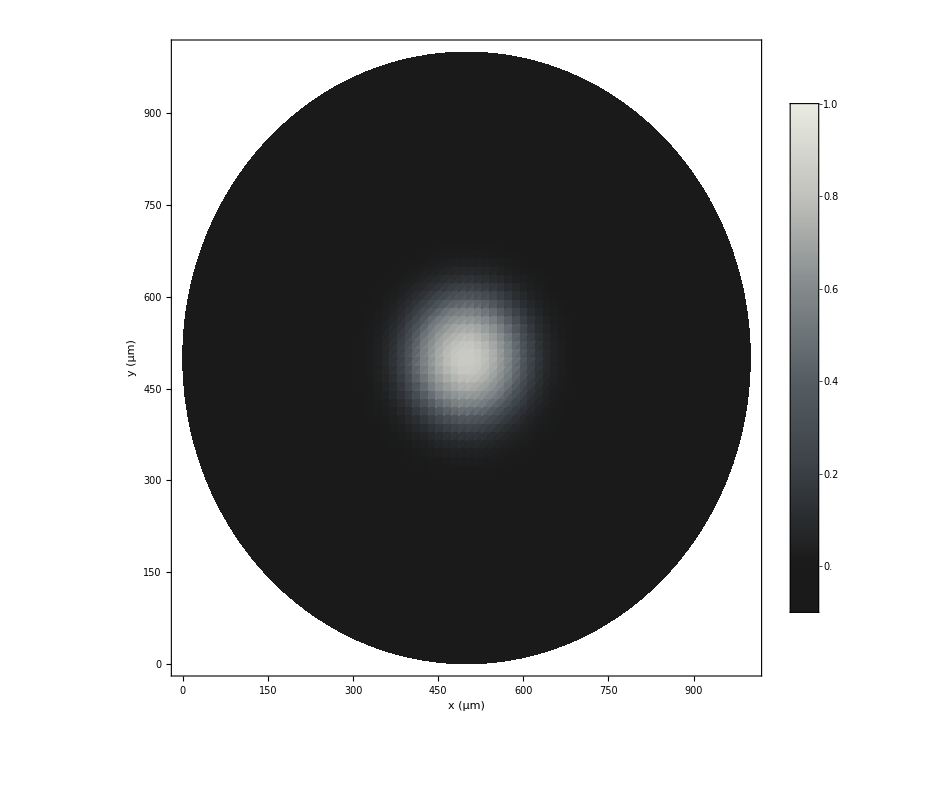

```mathematica
cf=ColorData["GrayTones"][#]&;

DensityPlot[CCSol[rFunc[x,y],2]/20,{x,0,xMax},{y,0,yMax},
PlotRange->{-0.1,1},
RegionFunction->Function[{x,y,z},(x-center[[1]])^2+(y-center[[2]])^2<rMax^2],
PlotPoints->75,
ImageSize->800,
PlotLegends->Placed[BarLegend[{cf,{-0.1,1}}],Right],
Axes->False,
ColorFunction->cf,
ColorFunctionScaling->False,
FrameLabel->{"x (μm)","y (μm)"}]
```

#### Single area tracking

```mathematica
CBTot[r_,t_]:=CBASol[r,t]+CBISol[r,t];
CBTotU[r_,t_]:=CBASol[r+uSol[r,t],t]+CBISol[r+uSol[r,t],t];


areaList = {};
start = r0;
Do[
rV = RadiusFunction[CBTot, t, 0.69,False,start, 0.5, 2];
AppendTo[areaList,Pi*rV^2];
If[rV < 10,start = r0,
start = rV];
,{t,0,tMax,1}]

(*areaList = {};
start = r0;
Do[
rV = RadiusFunction[CBTotU, t, 0.5,False,start, 0.95, 1.05];
AppendTo[areaList,Pi*rV^2];
If[rV < 10,start = r0,
start = rV];
,{t,0,tMax,1}]*)
```

a is 98.0557

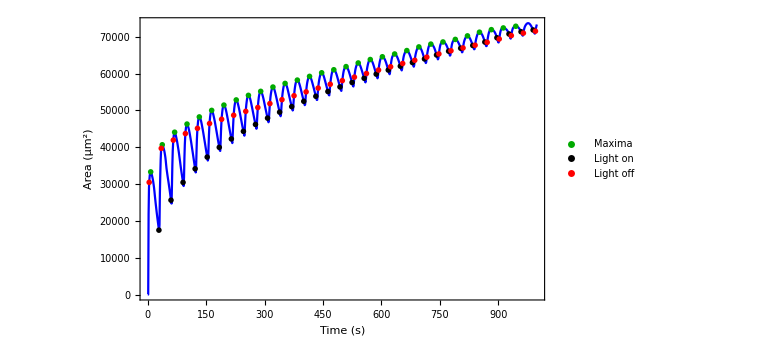

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];


maxT =tMax;
timeList = Range[maxT]-1 ;
data = Transpose[{timeList,areaList[[1;;maxT]]}];


off = 10*del;
timeListOn = Range[maxT]-1-off ;
timeListOff = Range[maxT]-1+off +len;
dataOnPoints = Quiet@Transpose[{timeListOn[[1;;maxT;;cyc]],areaInterp=Interpolation[data][timeListOn[[1;;maxT;;cyc]]]}];
dataOffPoints = Quiet@Transpose[{timeListOff[[1;;maxT;;cyc]],areaInterp=Interpolation[data][timeListOff[[1;;maxT;;cyc]]]}];

maxList = GetMaxima[data,30];

tFit1=30;
tFit2=150;
nlm=NonlinearModelFit[data[[tFit1;;tFit2]],a*x+b,{a,b},x];
Print["a is ",a/.nlm["BestFitParameters"]];

Legended[
Show[ 
ListPlot[data,Joined->True, PlotStyle->Directive[Blue], ImageSize->Large, PlotRange->Full,FrameLabel->{"Time (s)", "Area (μm^2)"}],
(*Plot[nlm[x],{x,tFit1,tFit2},PlotStyle->{Dashing[0.02],Orange,Thickness[0.008]}],*)
ListPlot[maxList, PlotMarkers->{Graphics[{Darker@Green,Disk[{0,0}]}],0.02}],
ListPlot[dataOnPoints, PlotMarkers->{Graphics[{Black,Disk[{0,0}]}],0.02}],
ListPlot[dataOffPoints, PlotMarkers->{Graphics[{Red,Disk[{0,0}]}],0.02}]],
Placed[PointLegend[{Darker@Green,Black,Red},{"Maxima","Light on","Light off"},LabelStyle->16],Scaled[{0.8,0.2}]]]
```

```mathematica
SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

gList = List[];
Do[

AppendTo[gList,
Show[
Plot[{CBASol[r,t]+CBISol[r,t] },{r,rMin,rMax},PlotRange->{-0.1,5}, PlotStyle->{Darker@Green}, FrameLabel->{"r (μm)","C_B (mM)"}, ImageSize->Large],
Plot[{0.7 },{r,rMin,rMax},PlotRange->{-0.1,5}, PlotStyle->{Thin,Black}, FrameLabel->{"r0","C_B (mM)"}],
ListPlot[{{Sqrt[data[[t+1,2]]/Pi],CBASol[Sqrt[data[[t+1,2]]/Pi],t]+CBISol[Sqrt[data[[t+1,2]]/Pi],t] }}, PlotStyle->Directive[Black,Large]],
Graphics[{Opacity[0.8*iFun[t]+0.05],Directive[Darker@Cyan],Rectangle[{0,0},{r0,100}]}],Graphics[{Text[Style["Time: "<>ToString[Floor[t,2]]<>" s",16],Scaled[{0.8,0.7}],{-1,0}]}]
]],
{t,0,0.8*maxT,1}]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Movies/beta_1.mp4",gList];
```

#### Multiple area tracking

```mathematica
rMin = 1;
rMax = 500;
tMax = 500;

width = 5;
r0 = 75;
len=1;
cyc = 30+len;
del=0.25;

(*import functions*)
Quiet@Get["/Users/csfloyd/Dropbox/Projects/TCB2Network/Mathematica/MidwayFiles/src/TCB2FunctionsCyl.m"]

interpListBase = "/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Dirs_r0_o/";
(*var = "beta";
vars = {"0.2", "0.6", "1.0"};*)

var = "r0";
vars = { "100","70","50"};

SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

pList = {};
th = 0.004;

Do[

interpList = Import[interpListBase <>var<>"_"<>ToString[vars[[i]]]<>"/sol.mx"];

CDISol = interpList[[1]];
CDASol = interpList[[2]];
CBISol = interpList[[3]];
CBASol = interpList[[4]];
CCSol = interpList[[5]];
CDSol = interpList[[6]];
CDstSol = interpList[[7]];
uSol = interpList[[8]];
vSol[r_,t_]:=Evaluate[D[uSol[r,tpp],tpp]/.tpp->t];

CBTot[r_,t_]:=CBASol[r,t]+CBISol[r,t];

(*areaList = {};
start = r0;
Do[
rV = RadiusFunction[CBTot, t, 0.69,False,start, 0.5, 2];
AppendTo[areaList,Pi*rV^2];
If[rV < 10,start = r0,
start = rV];
,{t,0,tMax,1}];*)


areaList = {};
start = r0;
Do[
rV = RadiusFunction[CBTotU, t, 0.5,False,start, 0.95, 1.05];
AppendTo[areaList,Pi*rV^2];
If[rV < 10,start = r0,
start = rV];
,{t,0,tMax,1}];

maxT =tMax;
timeList = Range[maxT]-1 ;
data = Transpose[{timeList,areaList[[1;;maxT]]}];

tFit1=30;
tFit2=150;
nlm=NonlinearModelFit[data[[tFit1;;tFit2]],a*x+b,{a,b},x];
Print["a is ",a/.nlm["BestFitParameters"]];



AppendTo[pList, 
Show[
ListPlot[data,Joined->True, PlotStyle->Directive[Thickness[th],ColorData["DarkRainbow",( i-1)/(Length[vars]-1)]], ImageSize->Large, PlotRange->Full,FrameLabel->{"Time (s)", "Area (μm^2)"}],
Plot[nlm[x],{x,tFit1,tFit2},PlotStyle->{Dashing[0.02],Orange,Thickness[0.008]}]
]
]

,{i,1,Length[vars]}]
```

a is 201.596

a is 145.78

a is 108.654

```mathematica
th = 0.004;

legend=LineLegend[
Table[Directive[Thickness[th],ColorData["DarkRainbow",( i-1)/(Length[vars]-1)]],{i,1,Length[vars]}]
,vars,LegendLayout->"Row", LegendLabel->"r_0",LabelStyle->{FontSize->16}];
```

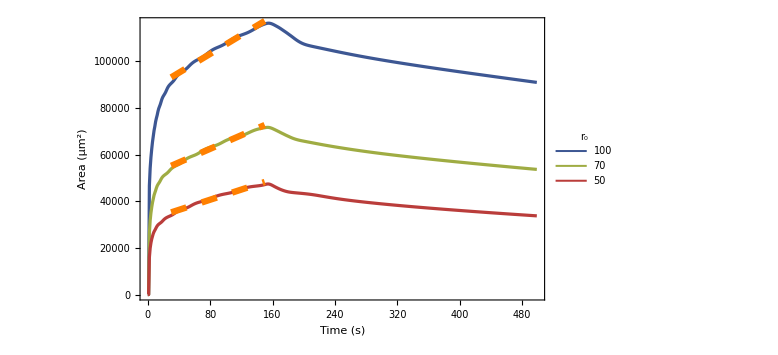

```mathematica
Legended[Show[pList],Placed[legend,{{0.5,0.2},{0.5,0.9}}]]
```

#### List plot multiple data

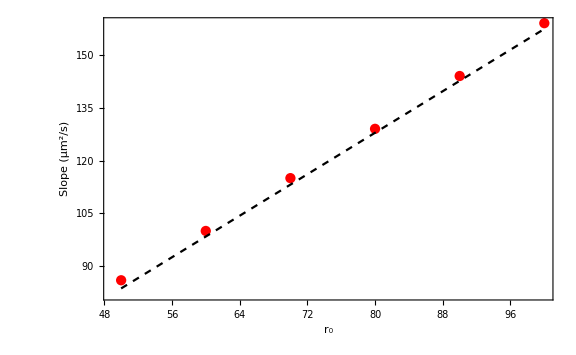

```mathematica
gData ={{50,86},{60,100},{70,115},{80,129},{90,144},{100,159}};
Show[
ListPlot[gData, FrameLabel->{"r_0", "Slope (μm^2/s)"},PlotStyle->Red,ImageSize->Large],
Plot[8*x*unit+10,{x,50,100}, PlotStyle->Directive[Black,Dashed]]]
```

{0.868172,0.361112,1.04638,1.4858,1.91776,2.21917,2.60073,2.96282,3.23109,3.4414,3.66797,3.88164,4.11904,4.3647,4.62185,4.85928,5.07312,5.26899,5.43648,5.56993,5.68494,5.78743,5.84381,5.9025,5.95261,5.99613,6.03553,6.07409,6.11604,6.15903,6.23065}

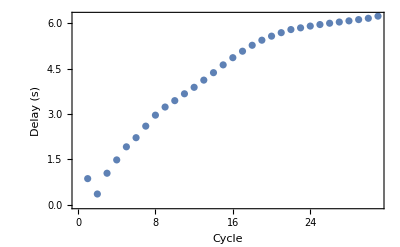

```mathematica
dels = maxList[[;;,1]] - dataOffPoints[[1;;30+1,1]]
ListPlot[dels, FrameLabel->{"Cycle", "Delay (s)"}]
```

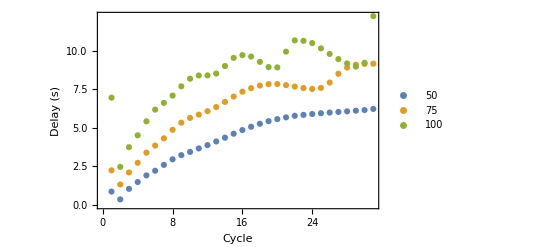

```mathematica
dels40={0.8681724777494013,0.361111992457559,1.0463804968571822,1.485802329496039,1.9177582324728633,2.219167810692994,2.600727287689665,2.962822165212941,3.2310854676415204,3.441403055409694,3.6679709938192673,3.881643251630692,4.119044714861047,4.364700317387417,4.621854994634475,4.859282828364769,5.073122886848353,5.268991384687411,5.436475452977334,5.569927372237544,5.684943734543026,5.787429629827557,5.843807984839259,5.902503577594985,5.952610764181941,5.996128488128875,6.035526224047544,6.074089329592425,6.11604197689644,6.1590269854541475,6.2306534918116085};dels60={2.245018014783181,1.3232121262896968,2.1078085076834583,2.7356119207336747,3.392511111036981,3.850942725660218,4.3221794186232785,4.8760706669605725,5.3390257754372215,5.646943800723136,5.863220518917956,6.084007448589773,6.352693391953778,6.687253386595387,7.033280732772937,7.350414413256033,7.579555895459237,7.745582750236622,7.838616464950405,7.8462486293002485,7.774985070503931,7.6801755527640125,7.5848969451481025,7.527472942818804,7.594639516990469,7.943093614863528,8.514442192787783,8.915939622656651,9.10306350236442,9.15554044172518,9.167827439640291};
dels100={6.963189699368275,2.468587352877364,3.746161776050826,4.5192339599474,5.425722537700551,6.186957325573616,6.62468646380043,7.099043297388619,7.697497268058896,8.191435996144264,8.401454085217779,8.408481673767369,8.524927914303134,9.01532839301143,9.54428074168186,9.721661925511228,9.62744229722125,9.28502409455075,8.949032344467355,8.927355949766593,9.948320405095956,10.679278074453919,10.65068702571125,10.505922740374103,10.161344138635059,9.79891388813337,9.466432982055949,9.186035762500296,8.978046429543724,9.227013723600521,12.25400978633229};

nn = 0;
ListPlot[{dels40/(40^nn),dels60/(60^nn),dels100/(100^nn)}, FrameLabel->{"Cycle", "Delay (s)"}, PlotLegends->{"50", "75", "100"}]
```

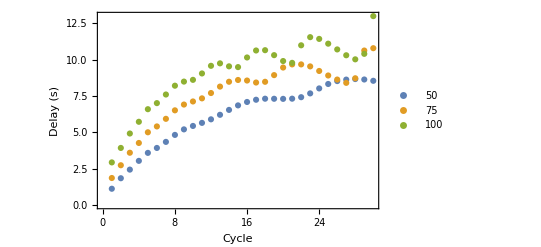

```mathematica
dels50={1.1150178053879003,1.8387246640259178,2.432718062005094,3.035558715563724,3.5852070328692776,3.924228006643318,4.341837840658712,4.823038278331126,5.2037602732322625,5.439684935322475,5.6512647645477045,5.895456489152139,6.207420632954552,6.544470185880584,6.855319395569381,7.090746754469251,7.243800676988371,7.315592667817896,7.31097879713991,7.3044927950097644,7.317187117303433,7.419273359998897,7.6809877245444795,8.023565374899931,8.32910608793577,8.529477006289426,8.630964407571923,8.668794834541131,8.638004495424411,8.548570159923543};
dels70={1.8546132328723033,2.733475646514364,3.594818330150062,4.267250183151788,5.0033789405848665,5.406045059863885,5.929881733790154,6.5146305144141365,6.913042065289176,7.125489108540478,7.339446929857218,7.706836736401328,8.149724607462247,8.483053114683003,8.604793203540964,8.5673713161666,8.429712811159334,8.480287043805447,8.939696950531129,9.46133085542374,9.678107230975797,9.677709949493533,9.539378810362223,9.22564079918891,8.913965573148971,8.634425474974478,8.407455568072578,8.72339207704772,10.632309465266871,10.793916135830159};
dels100={2.9289565155230903,3.925227651951573,4.919178631861584,5.7262583733408405,6.593099724460046,7.011511048016871,7.604485780508838,8.211167912453732,8.493849938996618,8.614198500586497,9.054285653778777,9.580487384940795,9.750054807112008,9.544377040581878,9.491687821471032,10.154796256619136,10.635802836958419,10.655991871196534,10.314600552591969,9.909080559501263,9.784575316494852,10.992953195962514,11.55367012958061,11.433689820924542,11.104934446080051,10.708813592266665,10.307011930517774,10.026481543906357,10.404964635054853,13.001798408780246};

nn = 0;
ListPlot[{dels50/(50^nn),dels70/(70^nn),dels100/(100^nn)}, FrameLabel->{"Cycle", "Delay (s)"}, PlotLegends->{"50", "75", "100"}]
```

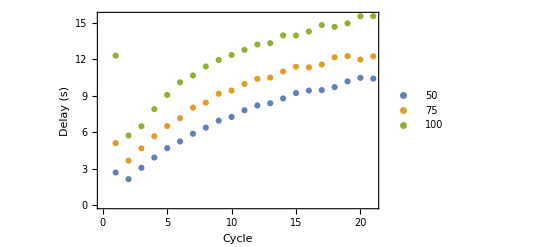

```mathematica
dels50={2.6778079927137393,2.129101942597565,3.060305335343969,3.9084140490625003,4.677873869040411,5.235077497810352,5.8683346951921465,6.371152838259178,6.95189925489052,7.257394057231181,7.805953951598724,8.201400238921906,8.382720927822447,8.78114145396205,9.220260563129216,9.42958113005227,9.464340125079502,9.71061324831146,10.185502878453804,10.475879608490004,10.414214744799665};
dels70={5.0941548938836885,3.6497513510065076,4.666548928577157,5.6601586907323025,6.500209435480912,7.1481720107288425,8.022501248447242,8.436653192959824,9.164466764514316,9.432219487996122,9.977842080498817,10.396076078054818,10.494429813360568,10.997428142715535,11.39840968671382,11.338700201379595,11.574075035619217,12.165444803209198,12.269202945871143,11.987377006003612,12.250296171748118};
dels110={12.307599261532312,5.723933298435213,6.487672992280977,7.898091745879469,9.070386156910388,10.110283927004957,10.671481661194377,11.415964365410673,11.94789649927202,12.363724304814582,12.787189306657865,13.226568818312956,13.333045441411343,13.975920165059222,13.969153828254036,14.298067592793132,14.827979087046174,14.6819657475354,14.973886211690797,15.55396099272491,15.565520860590937};
nn = 0;
ListPlot[{dels50/(50^nn),dels70/(70^nn),dels110/(110^nn)}, FrameLabel->{"Cycle", "Delay (s)"}, PlotLegends->{"50", "75", "100"}]
```

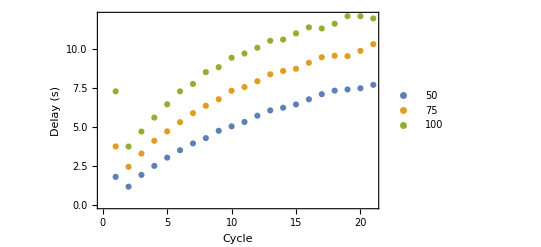

```mathematica
dels50={1.795058544294533,1.1695507337725104,1.920916891637276,2.499333319983151,3.027497930877871,3.500001021258754,3.9362388766032836,4.273771634935997,4.744720174809061,5.028251723379412,5.309101798584209,5.709531326212584,6.048669653333548,6.220115840819574,6.428417568678867,6.7576450521917195,7.0873043774813596,7.31244616061781,7.387502372396625,7.464504578477545,7.682451821715063};
dels70={3.7413485967579367,2.439064030809277,3.2884421514329176,4.103277595885174,4.705519593122972,5.295132795905346,5.875590117043828,6.345063019581318,6.761386088144377,7.303648781749871,7.541885831420018,7.915366007609691,8.355727404305867,8.567223816467447,8.71266425162321,9.095741772145573,9.44781853128353,9.545407360681907,9.518010535643725,9.857754467832592,10.284931579929548};
dels100={7.266058600981758,3.7345338679820443,4.694620094103811,5.587196310665178,6.438463629486847,7.26726027394534,7.743538445368841,8.498237828758818,8.812448651704017,9.418521667703999,9.68758366846464,10.054573732245501,10.503833656345819,10.582947197514557,10.973317591067087,11.361172351241066,11.291294935973667,11.593679124254095,12.079420807416682,12.074262447253204,11.931846104012948};

nn = 0;
ListPlot[{dels50/(50^nn),dels70/(70^nn),dels100/(100^nn)}, FrameLabel->{"Cycle", "Delay (s)"}, PlotLegends->{"50", "75", "100"}]
```

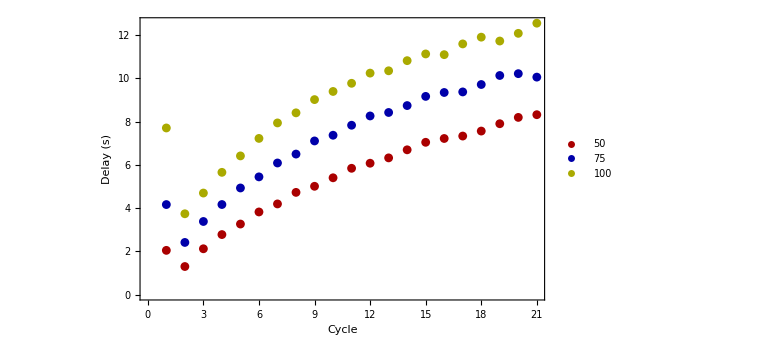

```mathematica
(* beta = 0 *)
dels50={2.044667117476643,1.296946451427253,2.1183575781880677,2.7753266067324347,3.262574374561069,3.8217557945930025,4.193426537654062,4.727680030503564,5.00930848367949,5.402909278278855,5.842301761058025,6.076508739512576,6.324256220749646,6.697414770976593,7.0450945840077,7.221352443855892,7.334070350252546,7.564898676223265,7.904602248658648,8.197047462645628,8.322277777441855};
dels70={4.1641044959415385,2.4111487970999264,3.3810157407068857,4.165832150783018,4.931462019916637,5.445407740162665,6.087695095219999,6.500003782189907,7.107837215003542,7.371828773113407,7.834500703495792,8.264062954953488,8.42494222843635,8.744460865542408,9.169394196563019,9.349938209875859,9.376247531681997,9.719030078032006,10.136509890240404,10.221196147876412,10.060872985395008};
dels100={7.708327690909714,3.737761024267016,4.696987643574062,5.655061964126702,6.4153770160696695,7.224919224567714,7.941577910385661,8.408318546386425,9.02102494920581,9.397667911444671,9.775328094951135,10.24638292151576,10.353956686384095,10.823006902318184,11.13372047184879,11.100229223220367,11.597826626989502,11.910135275116204,11.731062129455267,12.08665474562622,12.55714593692187};

nn = 0;
ListPlot[{dels50/(50^nn),dels70/(70^nn),dels100/(100^nn)}, FrameLabel->{"Cycle", "Delay (s)"}, PlotStyle->{Darker@Red,Darker@ Blue, Darker@Yellow},PlotLegends->Placed[{"50", "75", "100"},Scaled[{0.8,0.2}]], ImageSize->Large]
```

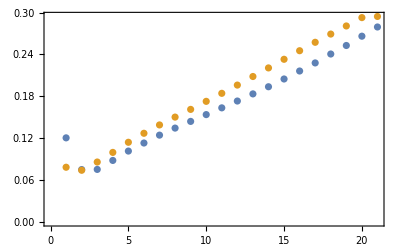

```mathematica
dels60={7.227357153670916,4.5000152282292945,4.513115069217065,5.2845538326468215,6.09144341729575,6.783179169847756,7.460661869747071,8.067210041235796,8.642043475907258,9.22680567789638,9.807589871821847,10.394412716033116,11.007197718272323,11.622504320270764,12.289437994153786,12.976103135349433,13.670607295742343,14.437275146921934,15.170048038546156,15.969469399175296,16.76148307400399};
dels90={7.049549575342271,6.660133815216312,7.723805291733285,8.962711071221761,10.271211467494197,11.430941861547126,12.507877400186999,13.519022997176592,14.512406359215959,15.550760491844756,16.58547987203991,17.648543911828313,18.754750513753493,19.86301275179602,20.975257010075552,22.08147289764446,23.167895001036072,24.229348753752333,25.27412957345689,26.352075878421374,26.50000649098422};
ListPlot[{dels60/60,dels90/90}]
```

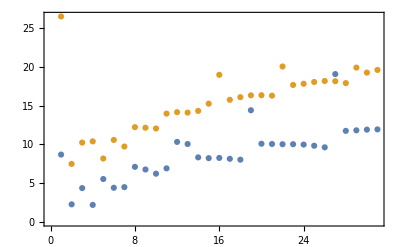

```mathematica
dels50={8.684889036158715,2.2646470735535686,4.359166322144574,2.192032071202263,5.529901802008595,4.403175442583944,4.48381749854002,7.101084668139947,6.760833776328866,6.219198729957498,6.904730626492494,10.318329072334166,10.047748427529939,8.322137414859867,8.224033081784,8.25184006217512,8.13876087244347,8.025851250919004,14.400826263576732,10.081252838663659,10.051489289321125,10.018368426822349,10.02048797908219,9.973655547259341,9.825057905366634,9.62039490396171,19.066302858259178,11.744305221992818,11.812997641276183,11.900267058873851,11.933968833220888};

dels100={26.50000029711093,7.483500120190278,10.230094525436982,10.384864430010822,8.176017733016408,10.573572272441794,9.72163944200895,12.223670583094616,12.14693752290458,12.05126322247827,13.969531970902267,14.153248861788825,14.097115011699827,14.318589509230208,15.252413447212746,18.972552655267066,15.748753617152488,16.087997642774326,16.326343796869764,16.34094957070954,16.285184673824347,20.048587208860567,17.666156278366998,17.82120065938136,18.048474348493983,18.174112745333673,18.147842255177807,17.905912131979107,19.902911197450067,19.258957322766037,19.603265631782847};

ListPlot[{dels50, dels100}]
```

```mathematica
dels50={0.41357645262703313,0.16539579743187005,0.6289960298869062,1.1443898642980344,1.1072597471437575,1.7797456541773045,1.8800546529952271,2.4869341699409233,2.328254100003676,2.8758070469230006,3.239719690418781,3.1661575540777562,3.6421890072383576,4.499942663929005,4.597642422864567,4.59768229655424,4.58048045913489,4.688764096575255,6.09705635446619,7.20805721838849,6.557405166803505,5.959670121339627,5.757330958933494,5.7543218803238005,5.774954509199802,5.792907139009003,5.791912679091865,9.314183534859922,6.971094621321868,6.739687894343547,6.645973511509624};
dels70 ={1.158809791545238,1.0408360794159108,1.2047881814075794,2.0430934520003916,2.750627320476582,2.9610932576937614,3.52115324262698,3.7909930268549203,4.24557095183215,4.351028794801493,5.1933212325863,5.3272817059282715,5.628359002317836,6.963410261619742,7.330962108032281,6.9533890887986445,7.041506723462817,7.277767382619004,9.902138881113729,8.254787068023575,7.984198782980911,8.077912060804579,8.027392090450462,7.92851687831444,9.934901323936629,8.956727756150372,8.806428674281847,8.662531584573799,8.48118226697477,14.779723384512636,9.923357345679506};
dels100={1.8724672819835675,2.614054795755848,3.2872848718206313,3.758095819036754,4.345092580067615,4.988650342870102,5.301297990321217,5.983697314981043,6.1988582820064835,7.270327628759901,7.321102096547008,8.07370534383358,9.499705099634468,8.836857318190141,9.367678887734485,10.901867955204978,9.95462611324001,10.102538392471956,10.140155853964416,10.329197982162441,10.708544934352858,10.921633892736963,10.729848505535983,10.472918684751448,11.911257091988318,11.744294154050522,11.405681550829058,11.126512819950335,16.883210731731765,13.044324244223503};
```

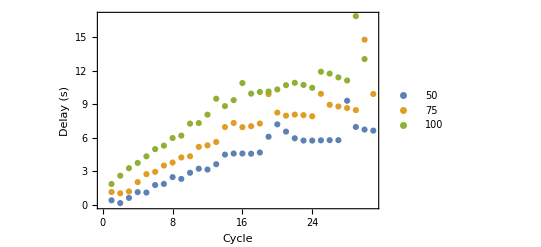

```mathematica
nn = 0;
ListPlot[{dels50/(50^nn),dels70/(70^nn),dels100/(100^nn)}, FrameLabel->{"Cycle", "Delay (s)"}, PlotLegends->{"50", "75", "100"}]
```

```mathematica
(10-4)/(80-10)
```

```mathematica
Manipulate[Show[
Plot[{CBASol[r,t],CBISol[
r,t],CBASol[r,t]+CBISol[r,t] },{r,rMin,rMax},PlotRange->{-1,4}],
ListPlot[{{Sqrt[data[[t+1,2]]/Pi],CBASol[Sqrt[data[[t+1,2]]/Pi],t]+CBISol[Sqrt[data[[t+1,2]]/Pi],t] }}]
],
{t,0,maxT,1}]
```

InterpolatingFunction::dmval: Input value {1.01019,736} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 737 of {{1,12815.},{2,15723.},{3,18083.8},{4,20074.8},{5,21405.3},{6,22910.7},{7,24167.5},{8,25497.},{9,26825.3},{10,27913.8},«571»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#### Diffusion accumulation plots

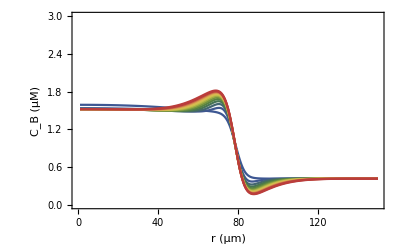

```mathematica
SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

functions = Evaluate[Table[CBISol[r,t]+CBASol[r,t],{t,len, tMax/2,2*cyc}]];
Plot[functions,{r,rMin,rMax},
PlotRange->{0,3},
FrameLabel->{"r (μm)","C_B (μM)"},
ImageSize->400,
PlotStyle->Table[ColorData["DarkRainbow", i/(Length[functions]-1)],{i,0,Length[functions]-1}]]
```

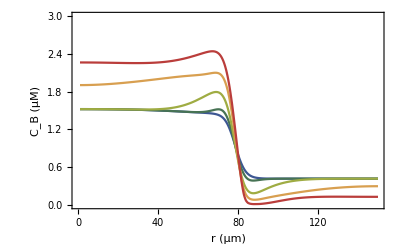

```mathematica
varList = {"-2","-1","0","1","2"};
functions = {};
tt = len+20*cyc;
Do[
var = varList[[i]];
interpList = Import["/Users/csfloyd/Dropbox/Projects/TCB2Network/Dirs/Dirs_cyl/Dirs_kIUnbind_DT_long/fac_List[1.0,"<>var<>"]/sol.mx"];
CBISol = interpList[[3]];
CBASol = interpList[[4]];
AppendTo[functions, CBISol[r,tt]+CBASol[r,tt]]

,{i,1,Length[varList]}
]

Plot[functions,{r,rMin,rMax},
FrameLabel->{"r (μm)","C_B (μM)"},
PlotRange->{0,3},
ImageSize->400,
PlotStyle->Table[ColorData["DarkRainbow", i/(Length[functions]-1)],{i,0,Length[functions]-1}]]
```

#### Contraction kymograph

```mathematica
CBTot[r_,t_]:=CBASol[r,t]+CBISol[r,t];
CBTotU[r_,t_]:=CBASol[r+uSol[r,t],t]+CBISol[r+uSol[r,t],t];


radList = {};
start = r0;
Do[
rV = RadiusFunction[CBTot, t, 0.69,False,start, 0.5, 2];
AppendTo[radList,rV];
If[rV < 10,start = r0,
start = rV];
,{t,0,tMax,1}]
```

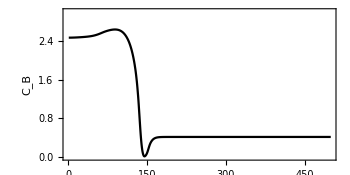
-Graphics- | 
-Graphics- |

```mathematica
SetOptions[DensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

rC = 0.4;
ul = rC;
(*ll = -rC;*)
ll = 0;
tup=500;
tl = 0;
tu = tup;

rl =1;
ru = 500;

maxT =tMax;
timeList = Range[tup]-1 ;
off = 10*del;
timeListOn = Range[maxT]-1-off ;
timeListOff = Range[maxT]-1+off +len;
dataOffPoints =timeListOff[[1;;maxT;;cyc]];

timeList = Range[maxT]-1 ;
data = Transpose[{radList[[1;;maxT]],timeList}];


cf=ColorData["ThermometerColors"][(#-ll)/(ul-ll)]&;

p= 60;
padding={{p,p/6},{p,p/6}};
paddingIns={{p,p/6},{p/2,p/6}};

size = 350;

(*scaleFunc[x_,a_,w_]:=x *(1+a Exp[-x^2/w]);*)
scaleFunc[x_,a_,w_]:=a Tanh[x/w];
scaleFunc[x_,a_,w_]:=a*Tanh[Abs[x/w]];

tC =tup;
pIns = Plot[CBASol[r,tC]+CBISol[r,tC],{r,rl,ru},PlotStyle->Black,
PlotRange->{0,3},FrameLabel->{None,"C_B"},
FrameTicks->Automatic,
ImageSize->size,
AspectRatio->1/2, 
ImagePadding->paddingIns];

legend = BarLegend[{cf,{ll,ul}},LegendLabel->"|v(r,t)|",
LabelStyle->{FontFamily->"Arial",Black,FontSize->16},
LegendMarkerSize->400(*, ColorFunctionScaling->True*)];

pF=Show[
DensityPlot[scaleFunc[vSol[r,t],rC,0.3],{r,rl,ru},{t,tl,tu}, 
PlotRange->{ll,ul},
PlotPoints->200,
AspectRatio->2,
ImageSize->size,
Axes->False,
ColorFunction->cf,
ColorFunctionScaling->False,
FrameLabel->{"r (μm)","Time (s)"},
ImagePadding->padding
],

ListLinePlot[data, PlotStyle->{Darker@Green}],
ParametricPlot[{50*iFun[t]+rl,t},{t,tl,tu},PlotPoints->200,PlotRange->{tl,tu},PlotStyle->Directive[Black,Thick]]

(*Plot[Table[dataOffPoints[[i]],{i,1,Length[dataOffPoints]}],{r,rl,ru},PlotStyle->Directive[Black]]*)
];
pCom=Grid[{{pIns,""},{pF,legend}}]
```

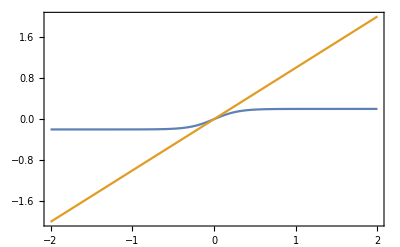

```mathematica
Plot[{.2Tanh[x/.3],x},{x,-2,2}]
```

```mathematica
Manipulate[Plot[Sign[vSol[r,t]*Log[Abs[vSol[r,t]]]],{r,1,rMax}],{t,0,tMax}]
```

InterpolatingFunction::dmval: Input value {0.2,112.} lies outside the range of data in the interpolating function. Extrapolation will be used.

#### Vector plot movie

```mathematica
center = {rMax,rMax};
rFunc[x_,y_]:=Sqrt[(x-rMax)^2+(y-rMax)^2]
rUnit[x_,y_]:=N[{x-rMax,y-rMax}/(Sqrt[(x-rMax)^2+(y-rMax)^2]+10^-3)];
pos[Ri_,t_,f_]:=Ri + f*uSol[rFunc[Ri[[1]],Ri[[2]]],t]*rUnit[Ri[[1]],Ri[[2]]];
pA[CBA_,CBI_]:=CBA/(CBA+CBI);


fac = 50;
xMax = 2*rMax;
yMax = 2*rMax;
Ris = DeleteCases[Flatten[Table[If[(i-center[[1]])^2+(j-center[[2]])^2<rMax^2,{i,j}],{i,0,xMax,xMax/fac},{j,0,yMax,yMax/fac}],1],Null];
Risl = Flatten[Table[{i,j},{i,0,xMax,xMax/fac},{j,0,yMax,yMax/fac}],1];
funcArray[t_]:=Table[{pos[Ris[[i]],t,2]},{i,1,Length[Ris]}]
sizeArray[t_]:=0.2*10^-2 Table[CBASol[rFunc[Ris[[i]][[1]],Ris[[i]][[2]]],t]+CBISol[rFunc[Ris[[i]][[1]],Ris[[i]][[2]]],t],{i,1,Length[Ris]}];

sigmoid[x_]:=1/(1+Exp[-x]);
smoothBump[x_,a_,xa_,xb_]:=sigmoid[(x-xa)/a]-sigmoid[(x-xb)/a]
waveFunc[t_,cyc_,len_,del_]:=Sum[smoothBump[t,del,cyc*i,cyc*i+len],{i,0,Floor[tMax/cyc]}];
```

0.0270712

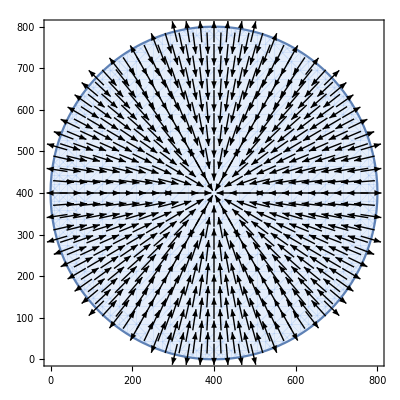

```mathematica
tt =100;
vMax = 1;
scaling=vSol[rFunc[#1,#2],tt]&;
maxSize = FindMaximum[Abs[vSol[r,tt]],{r,rMin,rMax}][[1]]
scale = 50;

VectorPlot[vSol[rFunc[x,y],tt]*rUnit[x,y],{x,0,xMax},{y,0,yMax},RegionFunction->Function[{x,y,z},(x-center[[1]])^2+(y-center[[2]])^2<rMax^2],VectorColorFunction->None,VectorPoints->Fine,VectorStyle->Directive[Black],VectorScale->{scaling,Large}]
```

```mathematica
SetOptions[DensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

cf=ColorData["LightTemperatureMap"][#]&;

ul = 6;
tl = 100;
tu = 131;
dt = 1;
vScale = 2;

gList = List[];
Do[
maxSize =Max[Abs[vSol[Range[rMin,rMax],t]]];
g = Show[
DensityPlot[CBASol[rFunc[x,y],t],{x,0,xMax},{y,0,yMax},
PlotRange->{-0.1,ul},
RegionFunction->Function[{x,y,z},(x-center[[1]])^2+(y-center[[2]])^2<rMax^2],
PlotPoints->150,
ImageSize->800,
PlotLegends->Placed[BarLegend[{cf,{-0.,ul}}],Right],
Axes->False,
ColorFunction->cf,
(*ColorFunctionScaling->False,*)
FrameLabel->{"x (μm)","y (μm)"}],

(*ListPlot[funcArray[t],AspectRatio->1,PlotRange->{{-1,xMax+1},{-1,yMax+1}},
BaseStyle->Black,
PlotStyle->(PointSize/@( sizeArray[t]))],*)

Graphics[{EdgeForm[{Thickness[0.008],Opacity[waveFunc[t,cyc,len,del]],Darker@Green}],FaceForm[{Opacity[0.5*waveFunc[t,cyc,len,del]],Darker@Green}],Disk[{xMax/2,yMax/2},r0]}],


(*VectorPlot[vSol[rFunc[x,y],t]*rUnit[x,y],{x,0,xMax},{y,0,yMax},RegionFunction->Function[{x,y,z},(x-center[[1]])^2+(y-center[[2]])^2<rMax^2],VectorColorFunction->None,VectorPoints->Fine,VectorStyle->Black,VectorScaling->Automatic]*)

VectorPlot[vSol[rFunc[x,y],t]*rUnit[x,y],{x,0,xMax},{y,0,yMax},RegionFunction->Function[{x,y,z},(x-center[[1]])^2+(y-center[[2]])^2<rMax^2],VectorColorFunction->None,VectorPoints->Fine,VectorStyle->Directive[Black],VectorScaling->"Log",VectorSizes->{0.1, vScale*maxSize}]

];

AppendTo[gList, g] 

,{t,tl,tu,dt}];
```

InterpolatingFunction::dmval: Input value {707.097,100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {707.107,100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {702.377,100} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Movies/NewTest4.mp4",gList];
```

#### Concentration video

```mathematica
SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

th = 0.004;


faint = 0.15;
opD=1;
opB = faint;
opC = 1;
opDT =faint;
label = "Ca^(2+) & DMNP";


gList = List[];
Do[


If[t==3*cyc,
opD = faint;
opB = 1;
opC = faint;
opDT = faint;
label="Bound TCB2";
];

If[t==6*cyc,
opD = faint;
opB = faint;
opC = faint;
opDT = 1;
label = "Diffusing TCB2";
];

If[t==9*cyc,
opD = 1;
opB = 1;
opC = 1;
opDT = 1;
label="Everything";
];

styles ={Directive[Blue,Thickness[th],Opacity[opD]],Directive[Darker@Green,Thickness[th],Opacity[opB]],Directive[Red,Thickness[th],Opacity[opDT]],Directive[Black,Thickness[th],Opacity[opC]],Directive[Blue,Dashed,Thickness[th],Opacity[opD]],Directive[Darker@Green,Dashed,Thickness[th],Opacity[opB]],Directive[Red,Dashed,Thickness[th],Opacity[opDT]]};

legend=LineLegend[styles,{"D/10","BA","DA","C","D^*/10","BI","DI"},LegendLayout->"Row"];



AppendTo[gList,
Show[
Plot[
{CDSol[r,t]/10,CBASol[r,t],CDASol[r,t],CCSol[r,t],CDstSol[r,t]/10 ,CBISol[r,t],CDISol[r,t]},
{r,rMin,rMax},
PlotStyle->styles,
PlotLegends->Placed[legend,{{0.6,.95},{0.5,1}}],
FrameLabel->{"r (μm)","Concentration (mM)"},
ImageSize->Large,
PlotRange->{{0,rMax},{-0.1,5}}],
Graphics[{Opacity[0.8*iFun[t]+0.05],Directive[Darker@Cyan],Rectangle[{0,0},{r0,100}]}],Graphics[{Text[Style["Time: "<>ToString[Floor[t,2]]<>" s",16],Scaled[{0.75,0.7}],{-1,0}]}],
Graphics[{Text[Style[label,16],Scaled[{0.75,0.6}],{-1,0}]}]

]
],
(*{t,0,8 * cyc,0.5}]*)
{t,0,12*cyc,0.5}]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/TCB2Network/Movies/ConcsSlow.mp4",gList];
```